```mathematica
T=({{1, 2, 3}, {3, -2, 1}, {2, -4, -2}})
```

{{1,2,3},{3,-2,1},{2,-4,-2}}

```mathematica
Inverse[IdentityMatrix[3]].T//MatrixForm
```

(1 | 2 | 3
3 | -2 | 1
2 | -4 | -2)

```mathematica
NullSpace[T]//MatrixForm
```

(-1 | -1 | 1)

```mathematica
T.{{-1},{-1},{1}}
```

{{0},{0},{0}}

```mathematica
NullSpace[Transpose[T]]
```

{{1,-1,1}}

```mathematica
Transpose[T].{{1},{-1},{1}}
```

{{0},{0},{0}}

```mathematica
S=({{1, 0, -1}, {0, 2, 3}, {-1, 3, 0}})
```

{{1,0,-1},{0,2,3},{-1,3,0}}

```mathematica
Solve[c1*({{1}, {0}, {-1}})+c2*({{0}, {2}, {3}})+c3*({{-1}, {3}, {0}})==({{1}, {0}, {0}}),{c1,c2,c3}]
```

{{c1→9/11,c2→3/11,c3→-2/11}}

```mathematica
Solve[c1*({{1}, {0}, {-1}})+c2*({{0}, {2}, {3}})+c3*({{-1}, {3}, {0}})==({{0}, {1}, {0}}),{c1,c2,c3}]
```

{{c1→3/11,c2→1/11,c3→3/11}}

```mathematica
Solve[c1*({{1}, {0}, {-1}})+c2*({{0}, {2}, {3}})+c3*({{-1}, {3}, {0}})==({{0}, {0}, {1}}),{c1,c2,c3}]
```

{{c1→-2/11,c2→3/11,c3→-2/11}}

```mathematica
ClearAll
```

ClearAll

```mathematica
A=({{1, -2}, {3, 4}})
```

{{1,-2},{3,4}}

```mathematica
B=({{0}, {0}})
H=({{1}, {1}})
L=({{1}, {0}})
R=({{0}, {1}})
```

{{0},{0}}

{{1},{1}}

{{1},{0}}

{{0},{1}}

```mathematica
A.({{0}, {0}})//MatrixForm
```

(0
0)

```mathematica
A.({{0}, {1}})//MatrixForm
```

(-2
4)

```mathematica
A.R//MatrixForm
```

(-2
4)

```mathematica
A.L//MatrixForm
```

(1
3)

```mathematica
V=({{x}, {y}})
```

{{x},{y}}

```mathematica
Solve[2^n == 31.5 * 10^12, {n}]
```

{{n→44.8404}}

```mathematica
A.V
```

{{x-2 y},{3 x+4 y}}

```mathematica
Solve[x-2*y == 3*x+4*y,{x, y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-x/3}}

```mathematica
Solve[x-2*y ==0 || 3*x+4*y == 0 ,{x, y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x/2},{y→-(3 x)/4}}

```mathematica
Solve[(x-2*y )* (3*x+4*y) == 1,{x, y} ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→1/8 (-x-√(-8+25 x^2))},{y→1/8 (-x+√(-8+25 x^2))}}

```mathematica
RegionPlot[-2<x-2*y <1&&0<3*x+4*y<7,{x, y}]
```

RegionPlot::argrx: RegionPlot called with 2 arguments; 3 arguments are expected.

RegionPlot[-2<x-2 y<1&&0<3 x+4 y<7,{x,y}]

```mathematica
A
```

{{1,-2},{3,4}}

```mathematica
Solve[A.({{x}, {y}}) && 0<x<1&& 0<y<1,{x,y}]
```

Solve::naqs: {{x-2 y},{3 x+4 y}}&&0<x<1&&0<y<1 is not a quantified system of equations and inequalities.

Solve[{{x-2 y},{3 x+4 y}}&&0<x<1&&0<y<1,{x,y}]

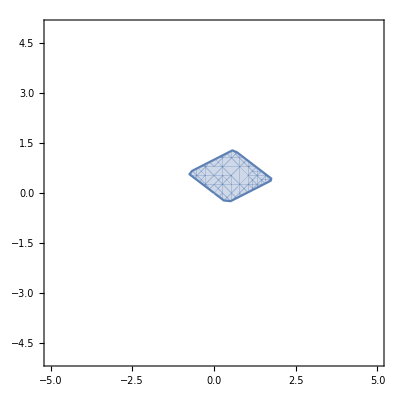

```mathematica
RegionPlot[-2<x-2y<1 && 0<3x+4y<7, {x,-5,5},{y,-5,5}]
```

```mathematica
points={{0,0},{-1,7},{-2,4},{1,3}};

reg=ConvexHullMesh@points
```

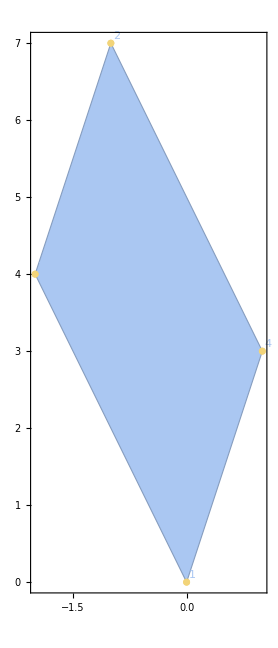

```mathematica
f[a_, b_, c_, d_]:= ConvexHullMesh@{({{a, b}, {c, d}}).{0,0},({{a, b}, {c, d}}).{1,0},({{a, b}, {c, d}}).{0,1},({{a, b}, {c, d}}).{1,1}}
```

```mathematica
pointt[a_, b_, c_, d_]:={({{a, b}, {c, d}}).{0,0},({{a, b}, {c, d}}).{1,0},({{a, b}, {c, d}}).{0,1},({{a, b}, {c, d}}).{1,1}}
```

```mathematica
Graphics[Point[pointt[2,0,0,2]]]
```

-Graphics-

```mathematica
Solve[ VectorAngle[{a+b,c+d},{b-a,d-c}]== 90 && b=1 &&a==2,{a, b, c, d}]
```

{}

```mathematica
f[1/2,1/2,1/2,1/2]
```

ConvexHullMesh::rnimpl: The function ConvexHullMesh is not implemented for {{0,0},{1/2,1/2},{1/2,1/2},{1,1}}.

ConvexHullMesh[{{0,0},{1/2,1/2},{1/2,1/2},{1,1}}]

```mathematica
ClearAll
```

ClearAll

SetDelayed::write: Tag List in {0, 0}[a_, b_, c_, d_] is Protected.

$Failed

SetDelayed::write: Tag List in {a,c}[a_,b_,c_,d_] is Protected.

$Failed

SetDelayed::write: Tag List in {b,d}[a_,b_,c_,d_] is Protected.

$Failed

SetDelayed::write: Tag List in {a+b,c+d}[a_,b_,c_,d_] is Protected.

$Failed

SetDelayed::pkspec1: The expression a_ cannot be used as a part specification.

$Failed

point

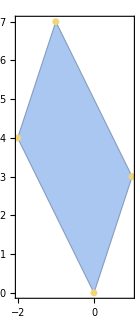

```mathematica
Clear[format];
format[plots_,s_: 12]:=TableForm[plots,TableHeadings->{TextCell[StringJoin[{"μ = ",ToString@#}],FontSize->s]&/@Range[-2,2],TextCell[StringJoin[{"σ = ",ToString@#}],FontSize->s]&/@{0.5,1,2,3,4}},TableAlignments->Center,TableSpacing->{1,1}]
```

```mathematica
parameters=Table[{i,j},{i,-2,2},{j,{0.5,1,2,3,4}}];
data=Map[RandomVariate[NormalDistribution@@#,1000]&,parameters,{2}];
Labeled[format[Map[ProbabilityPlot[#,NormalDistribution[0,1],PlotTheme->"Minimal",AspectRatio->1,ImageSize->100]&,data,{2}]],Style["Probability Plot of NormalDistribution",16],Top]
```

| σ = 0.5 | σ = 1 | σ = 2 | σ = 3 | σ = 4
μ = -2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = -1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = 0 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-Probability Plot of NormalDistribution

```mathematica
i=({{2, 1}})
```

{{2,1}}

```mathematica
j={2,3}
```

{2,3}

```mathematica
i.j
```

{7}

```mathematica
i={a,c}
```

{a,c}

```mathematica
j={b, d}
```

{b,d}

```mathematica
k={a+b,c+d}
```

{a+b,c+d}

```mathematica
Solve[Projection[i, j].j== 1,{a, b, c, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}}

```mathematica
{{c->(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}}/.Rule->Equal
```

{{c==(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}}

```mathematica
First[{{c->(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}}]
```

{c→(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}

```mathematica
c/.{{c->(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}}
```

{(b Conjugate[b]-a b^2 Conjugate[b]-a d^2 Conjugate[b]+d Conjugate[d])/((b^2+d^2) Conjugate[d])}

Dot::dotsh: Tensors {{8},{4}} and {{8},{4}} have incompatible shapes.

{{8},{4}}.{{8},{4}}

(x-2 y) (3 x+4 y)

```mathematica
Solve[{b, d}.{a, c}== 0 && Norm[{b, d}]== Norm[{a, c}],{a, b, c, d}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→c,d→-a},{b→-c,d→a},{b→0,c→0,d→-a},{b→0,c→0,d→a}}

```mathematica
Solve[Norm[{a,c}]^2+Norm[{b,d}]^2== Norm[{a+b, c+d}]^2 && a≠ 0 && b≠ 0 && c≠ 0 && d≠ 0,{a, b, c, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{}

```mathematica
Solve[{a,c}.{b,d}==0 &&{a,c}.{a+b,c+d}== 0, {a, b, c, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→-ⅈ c,d→ⅈ b},{a→ⅈ c,d→-ⅈ b},{a→0,c→0}}

```mathematica
Full=({{-5, -2.5}, {2.5, -5}})
```

Set::wrsym: Symbol Full is Protected.

{{-5,-2.5},{2.5,-5}}

ConvexHullMesh::rnimpl: The function ConvexHullMesh is not implemented for {{x-2 y},{3 x+4 y}}.

ConvexHullMesh[{{x-2 y},{3 x+4 y}}]

Region

```mathematica
Solve[{b, d}.{a, c}== 0 && Norm[{b, d}]== Norm[{a, c}],{a, b, c, d}]
```

{{b→c,d→-a},{b→-c,d→a},{b→0,c→0,d→-a},{b→0,c→0,d→a}}

```mathematica
Solve[{a,c}.{b,d}== 1 && {a,c}.{a+b,c+d}== 1,{a, b, c, d},Reals]
```

{}

```mathematica
Solve[a*b+c*d== 1 && a^2 + c^2 == 1,{a,b,c,d}]
```

{{a→-√(1-c^2),d→(1+b √(1-c^2))/c},{a→√(1-c^2),d→(1-b √(1-c^2))/c},{a→-1,b→-1,c→0},{a→1,b→1,c→0}}

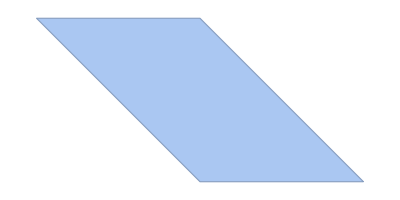

```mathematica
f[-1,-1,0,1]
```

```mathematica
Solve[Projection[{a+b,c+d},{a,c}]== Norm[{a,c}],{a, b, c, d}]
```

{(a ((a+b) Conjugate[a]+(c+d) Conjugate[c]))/(a Conjugate[a]+c Conjugate[c]),(c ((a+b) Conjugate[a]+(c+d) Conjugate[c]))/(a Conjugate[a]+c Conjugate[c])}

```mathematica
(* The incidence matrix of the circuit*)
```

```mathematica
({{-1, 1, 0, 0, 0, 0}, {0, -1, 1, 0, 0, 0}, {0, 0, -1, 1, 0, 0}, {1, 0, 0, -1, 0, 0}, {0, 0, -1, 0, 1, 0}, {0, 0, 0, 0, -1, 1}, {0, 0, 0, 1, 0, -1}}).({{x1}, {x2}, {x3}, {x4}, {x5}, {x6}})//MatrixForm
```

(-x1+x2
-x2+x3
-x3+x4
x1-x4
-x3+x5
-x5+x6
x4-x6)

```mathematica
({{b1}, {b2}, {b3}, {b4}, {b5}, {b6}, {b7}})
```

```mathematica
b=({{-6}, {6}, {0}, {0}, {0}, {-1}, {1}})
```

```mathematica
Transpose[({{-1, 1, 0, 0, 0, 0}, {0, -1, 1, 0, 0, 0}, {0, 0, -1, 1, 0, 0}, {1, 0, 0, -1, 0, 0}, {0, 0, -1, 0, 1, 0}, {0, 0, 0, 0, -1, 1}, {0, 0, 0, 1, 0, -1}})]//RowReduce//MatrixForm
```

(1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Solve[({{c1}, {c1}, {c1-c2}, {c1}, {c2}, {c2}, {c2}})=({{0}, {0}, {0}, {0}, {0}, {0}, {0}}),{c1,c2}]
```

Set::write: Tag Plus in 0-c2 is Protected.

Solve::ivar: 0 is not a valid variable.

Solve[{{0},{0},{0},{0},{0},{0},{0}},{0,0}]

```mathematica
Transpose[({{-1, 1, 0, 0, 0, 0}, {0, -1, 1, 0, 0, 0}, {0, 0, -1, 1, 0, 0}, {1, 0, 0, -1, 0, 0}, {0, 0, -1, 0, 1, 0}, {0, 0, 0, 0, -1, 1}, {0, 0, 0, 1, 0, -1}})]//RowReduce//MatrixForm
```

(1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ClearAll
```

ClearAll

```mathematica
Solve[ -y1+y4 == 0 && y1-y2== 0 &&  y2-y3-y5== 0&& y3-y4+y7== 0 && y5-y6 == 0 && y6-y7 == 0,{y1, y2, y3, y4, y5, y6, y7}]
```

{{y2→y1,y4→y1,y5→y1-y3,y6→y1-y3,y7→y1-y3}}

```mathematica
A=({{1, 2, 3}, {3, -2, 1}, {2, -4, -2}})//RowReduce//MatrixForm
```

```mathematica
({{1, 0, 1}, {0, 1, 1}, {0, 0, 0}})-> {({{1}, {3}, {2}}),({{2}, {-2}, {-4}})}
```

```mathematica
Transpose[({{1, 2, 3}, {3, -2, 1}, {2, -4, -2}})]//MatrixForm
```

```mathematica
({{1, 3, 2}, {2, -2, -4}, {3, 1, -2}})//RowReduce//MatrixForm
```

(1 | 0 | -1
0 | 1 | 1
0 | 0 | 0)

```mathematica
Solve[-x2+x3==6&& x4-x6==1&&x1-x4==0&&-x3+x5== 0, {x1, x2, x3, x4, x5, x6}]
```

{{x3→6+x2,x4→x1,x5→6+x2,x6→-1+x1}}

```mathematica
Solve[3*c2+5*(c1-c2)== -6 && 3*(c1-c2)+4*c2== -7, {c1, c2, c3}]
```

Solve::ivar: 0 is not a valid variable.

Solve[False,{0,0,c3}]

```mathematica
ClearAll
```

ClearAll

```mathematica
Solve[({{5, 3}, {3, 4}}).{cc3, cc2}== ({{6}, {7}}),{cc3, cc2}]
```

{{cc3→3/11,cc2→17/11}}